# Ambient Air Isoprene Section 1: Set-up details Section 2: Import Data and Check Quality Section 3: Calibration chromatograms Section 4: Sample 1 (S) Chromatograms Section 5: Sample 2 (X) Chromatograms

## Section 1: Set-up Details In this section, enter the different conditions for the experiment. In your directory, you require all the raw chromatograms to be in a folder called "Raw Chroms" with no other files.

```mathematica
(*Enter the directory path, "Conor Bolas" on Hyskeir, "cgb36" on Askival*)
directory="C:\\Users\\cgb36\\Dropbox (Cambridge University)\\iDirac - Wytham\\Walkway_Final\\Week 20";
(*Enter the calibration gas concentration*)
mrcal  = 11.61166;
(*Enter a value in the chromatogram, below which indicates a dip in the signal that indicates a fault*)
drop=1550;
(*Enter the computer that last run the script - Hyskeir or Askival*)
"Askival";
(*Enter the colour iDirac Used - Yellow, Grey or Orange*)
"Orange";
(*Enter the date the script was ran*)
"03/12/2018";
(*Enter the calibration Torpedo used - Connie, Jambo, Wallace, Floss, Crystal or the NPL one*)
"Crystal";
(*Enter here a brief description of the experiment*)
"This is Week 20 of data for the walkway instrumnet at Wytham Woods for the WISDOM field campiagn 2018. This script is analysing the data of Inlet 3 and Inlet 4 in the upper reaches of the canopy.";
(*Where is Sample 1 (S) located?*)
"It inlet is at the walkway - Inlet 3 - height 13.17m";
(*Where is Sample 2 (X) located?*)
"This inlet is sampling from just above the canopy - Inlet 4 - height 15.55m";
```

## Section 2: Import Data and Check Quality Read in data and Remove Anomalous Files This section reads in the data and examines whether the files are the correct length, if they are not they are printed at the end of this block - they can be manually cut & pasted into a "Bad Chroms" folder in the directory. It also looks at the minimum data point of each files' data series and if this data point is lower than the value of the variable ' drop' then it removes from the list of chromatograms to continue the script with only the ' good' chroms. An instrument fault would cause this drop in the signal. These are also printed at the end of the block and these can be manually cut & pasted into a "Bad Chroms" folder in the directory. These files may be useful later.

```mathematica
rawdir=StringJoin[directory,"\\Raw Chroms"];
SetDirectory[rawdir];
fxq= FileNames["*CSV*"]; 


(*This small block identifies the good files, fx is a list of the filenames of the 'good' files*)
dum=Table[0,{i,Length[fxq]}];
Monitor[Do[test=Import[fxq[[i]],"csv"][[17;;]];
test2=Select[Import[fxq[[i]],"csv"][[245;;]],Min[#[[2]]]<drop&];
Length[test2];
If[Length[test2]==0,dum[[i]]=fxq[[i]]];x1=N[(i/3)/nn],{i,Length[dum]}]
fx=Select[dum,#=!=0&];

(*This small block identifies the bad files, fxbad is a list of the filenames of the 'bad' files*)
dumbad=Table[0,{i,Length[fxq]}];
Do[test=Import[fxq[[i]],"csv"][[17;;]];
test2=Select[Import[fxq[[i]],"csv"][[245;;]],Min[#[[2]]]<drop&];
Length[test2];
If[Length[test2]=!=0,dumbad[[i]]=fxq[[i]]];x1=N[((i+0.33)/2)/nn],{i,Length[dumbad]}]
fxbad=Select[dumbad,#=!=0&];

(*This small block makes a table with all the good files data*)
nn=Length[fx];
type= Table[{},{i,Length[fx]}];
data= Table[{},{i,Length[fx]}];
Do[xdum = Import[fx[[i]],"CSV"];
data[[i]]=xdum;
type[[i]]=xdum[[3,2]];x1=N[((i+0.66)/1)/nn],{i,Length[fx]}],ProgressIndicator[x1]]

Print["This is the numer of files:                            ",Length[fxq]]
Print["There are this many 'good' chroms:                     ",Length[fx]]
Print["There are this many 'bad' chroms with a signal drop:   ", Length[fxq]-Length[fx]]
Print["These are the 'bad' chrom numbers:                     ", fxbad]
```

This is the numer of files:                            408

There are this many 'good' chroms:                     408

There are this many 'bad' chroms with a signal drop:   0

These are the 'bad' chrom numbers:                     {}

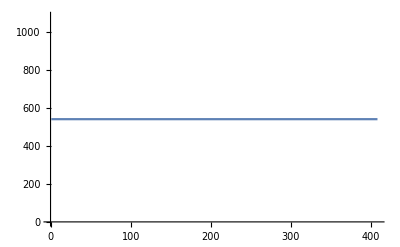

```mathematica
ListLinePlot[Table[Length[data[[i]]],{i,Length[data]}]]
```

```mathematica
Print["The chromatograms are meant to be this long: ",Length[data[[1]]]]
Print["If they are shorter than this, they have been truncated due to instrumment defects. They need to be cut&pasted into the 'Bad Chroms' folder so that they don't cause errors later in the script. If there are no files listed, then no action is needed. The files that have been truncated are listed here:"]
Do[If[Length[data[[i]]]<542,Print[fx[[i]]]],{i,Length[data]}]
```

The chromatograms are meant to be this long: 542

If they are shorter than this, they have been truncated due to instrumment defects. They need to be cut&pasted into the 'Bad Chroms' folder so that they don't cause errors later in the script. If there are no files listed, then no action is needed. The files that have been truncated are listed here:

```mathematica
(*This block tells you the date and time of the first and last file*)
firstfile=data[[1]];first=AbsoluteTime[firstfile[[2,2;;7]]];
lastfile=data[[-1]];last=AbsoluteTime[lastfile[[2,2;;7]]];
DateString[first]
DateString[last]
```

Wed 10 Oct 2018 12:55:36

Tue 23 Oct 2018 12:58:37

## Section 3: Calibration Chromatograms

### This section - Takes the calibration chromatograms - Plots them - Integrates the peak - Uses the peak height, volume and mixing ratio to construct a calibration curve

Section 3.1

### Select the Calibration Chromatograms and plot them, along with the sample volume to diagnose errors. The bottom two lines check the chromatogram number of the error files. You need to select the peak window upper and lower limits from the plot of all the chromatograms.

```mathematica
SetDirectory[directory];
```

```mathematica
cno = {};
Do[If[type[[i]]=="C",cno = Append[cno,i]],{i,Length[fx]}]
```

```mathematica
calchrom = Table[{},{i,Length[cno]}];
volc = Table[{},{i,Length[cno]}];
chromnoc = Table[{},{i,Length[cno]}];
timec= Table[{},{i,Length[cno]}];
off=150;
```

```mathematica
Do[dumx = data[[cno[[i]]]];
calchrom[[i]]=Table[dumx[[j,2]],{j,17+off,Length[dumx]}];
volc[[i]]=dumx[[11,2]];
chromnoc[[i]]=dumx[[1, 2]];
timec[[i]]  =dumx[[2,2;;7]];,{i,Length[cno]}]
```

```mathematica
timecab=Table[AbsoluteTime[timec[[i]]],{i,Length[timec]}];
```

```mathematica
timecdays=(timecab-timecab[[1]])/24./3600;
```

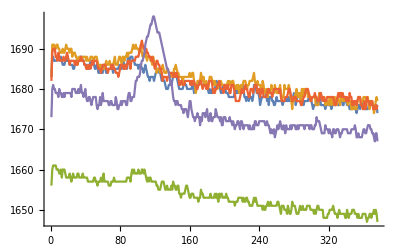

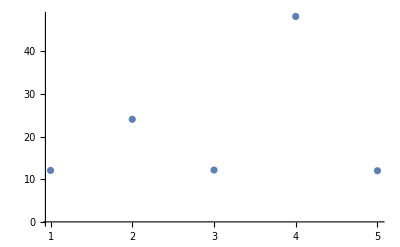

```mathematica
ListLinePlot[calchrom,PlotRange->All]
ListPlot[volc,PlotRange->All]
```

```mathematica
Do[If[Max[volc[[i]]]>20000,Print[chromnoc[[i]]]],{i,Length[calchrom]}]
Do[If[Max[volc[[i]]]<2,Print[chromnoc[[i]]]],{i,Length[calchrom]}]
```

Section 3.2

### This section integrates the calibration peaks using a peak finding function. There is also a function to estimate the background. Plotted below are the fitting functions, scatter-plots of the fit and the baseline/data relationship and a plot of the peak positions. A CSV file is generated "calibrations.csv" that contains all this data.

```mathematica
resultsc=Table[{},{i,cno}];
```

```mathematica
Manipulate[dumxxb=EstimatedBackground[MeanFilter[calchrom[[jj]],5],20];diff=calchrom[[jj]]-dumxxb;
peaksx=FindPeaks[diff,5,0,Max[diff]/2];
peaks=peaksx[[1]];
ff=FindFit[diff,a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{{a,0},{b,0},{bb,0},{c,peaks[[2]]},{d,peaks[[1]]},{e,10}},i,MaxIterations->100];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitbase = Table[af+bf*i+bbf*i^2,{i,Length[diff]}];fitpeak= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[diff]}];
ListLinePlot[{diff,fitbase,fitpeak},PlotRange->All,PlotLabel->{{"Cal Chrom Number:",chromnoc[[jj]],"Index Number:",jj}}],{jj,1,Length[cno],1}]
```

```mathematica
peaks=peaksx[[1]]
```

{36,2.73675}

```mathematica
Manipulate[dumxxb=EstimatedBackground[MeanFilter[calchrom[[jj]],5],20];diff=calchrom[[jj]]-dumxxb;
peaksx=FindPeaks[diff,5,0,Max[diff]/2];
peaks=peaksx[[1]];
ff=FindFit[diff,a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{{a,0},{b,0},{bb,0},{c,peaks[[2]]},{d,peaks[[1]]},{e,10}},i,MaxIterations->100];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitbase = Table[af+bf*i+bbf*i^2,{i,Length[diff]}];fitpeak= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[diff]}];
fitted = fitpeak-fitbase;
measured = diff-fitbase;
scatterdata=Table[{fitted[[jj]],measured[[jj]]},{jj,Length[fitpeak]}];
lm=LinearModelFit[scatterdata,x,x];
graderr = lm["ParameterTable"][[1,1,3,3]];
ListPlot[scatterdata,PlotRange->All,PlotLabel->{{"Chrom Number:",chromnoc[[jj]],"Index:",jj,"Error:",graderr}}],{jj,1,Length[cno],1}]
```

```mathematica
Do[dumxxb=EstimatedBackground[MeanFilter[calchrom[[jj]],5],20];diff=calchrom[[jj]]-dumxxb;
peaksx=FindPeaks[diff,5,0,Max[diff]/2];
peaks=peaksx[[1]];
ff=FindFit[diff,a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{{a,0},{b,0},{bb,0},{c,peaks[[2]]},{d,peaks[[1]]},{e,10}},i,MaxIterations->100];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitbase = Table[af+bf*i+bbf*i^2,{i,Length[diff]}];fitpeak= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[diff]}];
fitted = fitpeak-fitbase;
measured = diff-fitbase;
area=Mean[fitpeak]-Mean[fitbase];
residual=diff-fitpeak;
rms=StandardDeviation[residual];
scatterdata=Table[{fitted[[jj]],measured[[jj]]},{jj,Length[fitpeak]}];
lm=LinearModelFit[scatterdata,x,x];
graderr = lm["ParameterTable"][[1,1,3,3]];
(*These lines add a Igor-compatable datetime format*)
timecigor = Table[DateString[timecab[[jj]],{"Day", "/","Month","/","Year", " ", "Hour", ":", "Minute", ":", "Second"}],{jj,Length[timecab]}];
resultsc[[jj]]=Flatten[{cno[[jj]],timecab[[jj]],timecigor[[jj]],chromnoc[[jj]],volc[[jj]],df,cf,ef,area,graderr,rms}] ,
{jj,Length[cno]}]
```

```mathematica
headers = {"Index", "Abs_Time","Igor_time", "Chrom_No", "Volume", "Position", "Peak_Height", "Peak_Width","Peak_Area",  "Gradient_Error", "Root_Mean_Square_Error"};
headedoutputco = Prepend[resultsc,headers];
Export["calibrations.csv", headedoutputco];
```

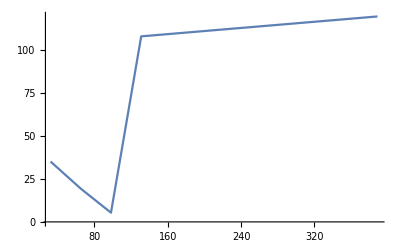

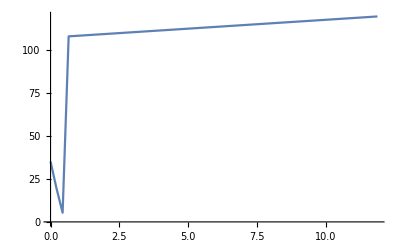

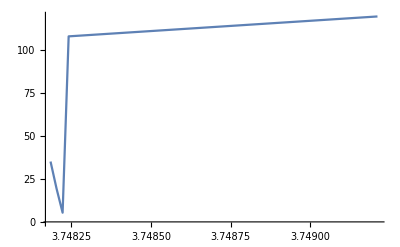

```mathematica
(*calposx=Table[resultsc[[i,5]],{i,Length[resultsc]}];*)
calposindex= Table[{resultsc[[i,1]],resultsc[[i,6]]},{i,Length[resultsc]}];
calposdays = Table[{timecdays[[i]],resultsc[[i,6]]},{i,Length[resultsc]}];
calposabs = Table[{timecab[[i]],resultsc[[i,6]]},{i,Length[resultsc]}];
(*calpos = calposy;*)
ListLinePlot[calposindex,PlotRange->All]
ListLinePlot[calposdays,PlotRange->All]
ListLinePlot[calposabs,PlotRange->All]
```

```mathematica
calposabsi=Interpolation[calposabs,InterpolationOrder->1];
calposindexi=Interpolation[calposindex,InterpolationOrder->1];
```

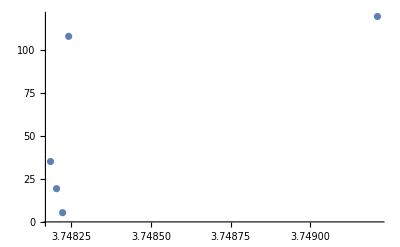

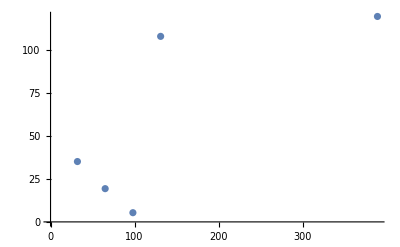

```mathematica
ListPlot[calposabsi]
ListPlot[calposindexi]
```

Section 3.3

### Select the Blank Chromatograms and plot them, along with the sample volume to diagnose errors. The bottom two lines check the chromatogram number of the error files. You need to select the peak window upper and lower limits from the plot of all the chromatograms.

```mathematica
SetDirectory[directory];
```

```mathematica
bno = {};
Do[If[type[[i]]=="B",bno = Append[bno,i]],{i,Length[fx]}]
```

```mathematica
blankchrom = Table[{},{i,Length[bno]}];
volb = Table[{},{i,Length[bno]}];
chromnob = Table[{},{i,Length[bno]}];
timeb= Table[{},{i,Length[bno]}];
```

```mathematica
Do[dumx = data[[bno[[i]]]];
blankchrom[[i]]=Table[dumx[[j,2]],{j,17+off,Length[dumx]}];
volb[[i]]=dumx[[11,2]];
chromnob[[i]]=dumx[[1, 2]];
timeb[[i]]  =dumx[[2,2;;7]];,{i,Length[bno]}]
```

```mathematica
timebab=Table[AbsoluteTime[timeb[[i]]],{i,Length[timeb]}];
```

```mathematica
timebdays=(timebab-timebab[[1]])/24./3600;
```

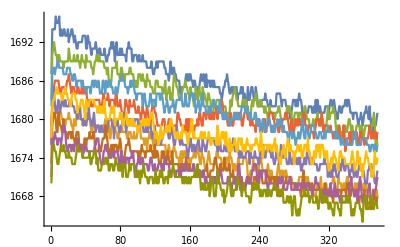

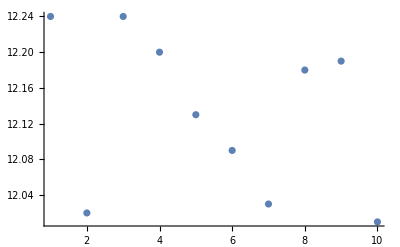

```mathematica
ListLinePlot[blankchrom,PlotRange->All]
ListPlot[volb,PlotRange->All]
```

```mathematica
Do[If[Max[volb[[i]]]>20000,Print[chromnob[[i]]]],{i,Length[blankchrom]}]
Do[If[Max[volb[[i]]]<2,Print[chromnob[[i]]]],{i,Length[blankchrom]}]
```

Section 3.4

### This section integrates the blank peaks using a peak finding function. There is also a function to estimate the background. Plotted below are the fitting functions, scatter-plots of the fit and the baseline/data relationship and a plot of the peak positions. A CSV file is generated "calibrations.csv" that contains all this data.

```mathematica
resultsb=Table[{},{i,bno}];
```

```mathematica
cals=Table[{resultsc[[i,2]],resultsc[[i,6]]},{i,Length[cno]}];
```

```mathematica
Clear[ncentre]
```

```mathematica
(*This function looks for the extrapolated points and sets them to the first or last calibration positions*)
ncentre[n_]:=If[n<cno[[1]],bcentre=cno[[1]], If[n>cno[[-1]],bcentre=cno[[-1]],bcentre=n]]
```

```mathematica
Manipulate[dl=calposindexi[N[ncentre[bno[[jj]]]]]-20;
dh=calposindexi[N[ncentre[bno[[jj]]]]]+20;
mnx=Mean[blankchrom[[jj]]];

ff=FindFit[blankchrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mnx-200<a<mnx+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeakb= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[blankchrom[[jj]]]}];
fitbaseb= Table[af+bf*i+bbf*i^2,{i,Length[blankchrom[[jj]]]}];

ListLinePlot[{blankchrom[[jj]],fitbaseb,fitpeakb},PlotRange->All,PlotLabel->{{"Cal Chrom Number:",chromnob[[jj]],"Index Number:",jj}}],{jj,1,Length[bno],1}]
```

```mathematica
Manipulate[dl=calposindexi[N[ncentre[bno[[jj]]]]]-20;
dh=calposindexi[N[ncentre[bno[[jj]]]]]+20;
mnx=Mean[blankchrom[[jj]]];
ff=FindFit[blankchrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mnx-200<a<mnx+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeakb= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[blankchrom[[jj]]]}];
fitbaseb= Table[af+bf*i+bbf*i^2,{i,Length[blankchrom[[jj]]]}];

fitted = fitpeakb-fitbaseb;
measured = blankchrom[[jj]]-fitbaseb;
scatterdata=Table[{fitted[[jj]],measured[[jj]]},{jj,Length[fitpeakb]}];
lm=LinearModelFit[scatterdata,x,x];
graderr = lm["ParameterTable"][[1,1,3,3]];
ListPlot[scatterdata,PlotRange->All,PlotLabel->{{"Chrom Number:",chromnob[[jj]],"Index:",jj,"Error:",graderr}}],{jj,1,Length[bno],1}]
```

```mathematica
Do[dl=calposindexi[N[ncentre[bno[[jj]]]]]-20;
dh=calposindexi[N[ncentre[bno[[jj]]]]]+20;
mnx=Mean[blankchrom[[jj]]];

ff=FindFit[blankchrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mnx-200<a<mnx+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeakb= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[blankchrom[[jj]]]}];
fitbaseb= Table[af+bf*i+bbf*i^2,{i,Length[blankchrom[[jj]]]}];

fitted = fitpeakb-fitbaseb;
measured = blankchrom[[jj]]-fitbaseb;
area=Mean[fitpeakb]-Mean[fitbaseb];
residual=blankchrom[[jj]]-fitpeakb;
rms=StandardDeviation[residual];
scatterdata=Table[{fitted[[jj]],measured[[jj]]},{jj,Length[fitpeakb]}];
lm=LinearModelFit[scatterdata,x,x];
graderr = lm["ParameterTable"][[1,1,3,3]];
(*These lines add a Igor-compatable datetime format*)
timebigor = Table[DateString[timebab[[jj]],{"Day", "/","Month","/","Year", " ", "Hour", ":", "Minute", ":", "Second"}],{jj,Length[timebab]}];
resultsb[[jj]]=Flatten[{bno[[jj]],timebab[[jj]],timebigor[[jj]],chromnob[[jj]],volb[[jj]],df,cf,ef,area,graderr,rms}] ,
{jj,Length[bno]}]
```

```mathematica
headers = {"Index", "Abs_Time","Igor_time", "Chrom_No", "Volume", "Position", "Peak_Height", "Peak_Width","Peak_Area",  "Gradient_Error", "Root_Mean_Square_Error"};
headedoutputco = Prepend[resultsb,headers];
Export["blanks.csv", headedoutputco];
```

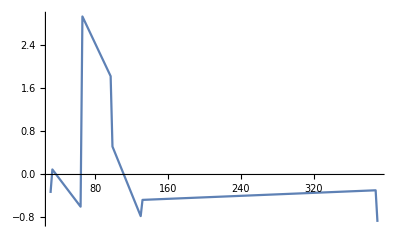

```mathematica
(*calposx=Table[resultsc[[i,5]],{i,Length[resultsc]}];*)
blankph= Table[{resultsb[[i,1]],resultsb[[i,7]]},{i,Length[resultsb]}];
(*calpos = calposy;*)
ListLinePlot[blankph,PlotRange->All]
```

Section 3.5

### This section takes the blank runs and adds this to the existing calibration data for a more accurate cal curve.

```mathematica
(*These lines add the concentration of the input gas - 0 for blanks and the cal gas conc for cals*)
Do[AppendTo[resultsb[[j]],0],{j,0,Length[resultsb]}]
Do[AppendTo[resultsc[[j]],mrcal],{j,0,Length[resultsc]}]
```

AppendTo::normal: Nonatomic expression expected at position 1 in AppendTo[resultsb⟦j⟧,0].

AppendTo::normal: Nonatomic expression expected at position 1 in AppendTo[resultsc⟦j⟧,11.6117].

```mathematica
resultscandb=Join[resultsb,resultsc];
```

Section 3.6

### The Calibration Curves This section looks at the calibration data and constructs two calibrations plots, one based on peak height and one based on peak area. The line it plots is linear, with a set-intercept at 0.

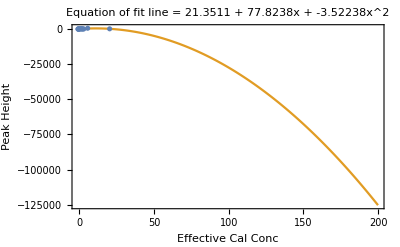

```mathematica
(*This draws a plot of peak height vs calvol*mr of the cal cylinder*)
phscatt=Table[{resultscandb[[i,7]],resultscandb[[i,5]]*resultscandb[[i,12]]},{i,2,Length[resultscandb]}];
phfit =FindFit[phscatt,a + b*i +c*i^2,{a,b,c},i];
phaf=phfit[[1,2]];
phbf = phfit[[2,2]];
phcf=phfit[[3,2]];
phfitted = Table[{i,phaf + phbf*i +phcf*i^2},{i,0,200}];
ListPlot[{phscatt,phfitted},Joined->{False,True},PlotRange->All,PlotLabel->StringJoin["Equation of fit line = ",ToString[phaf]," + ",ToString[phbf],"x"," + ",ToString[phcf],"x^2"],Frame->{{True,False},{True,False}}, FrameLabel->{Style["Effective Cal Conc",Black,Medium],Style["Peak Height",Black,Medium]}]
```

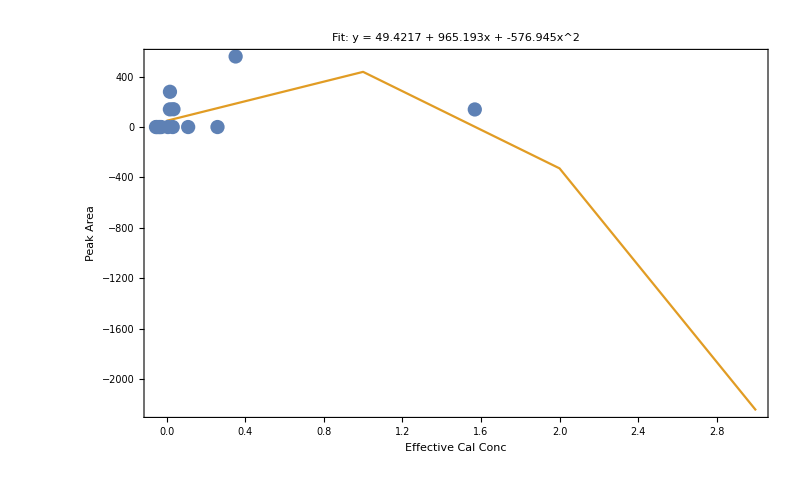

```mathematica
(*This draws a plot of peak area vs calvol*mr of the cal cylinder*)
ascatt=Table[{resultscandb[[i,9]],resultscandb[[i,5]]*resultscandb[[i,12]]},{i,2,Length[resultscandb]}];
afit =FindFit[ascatt,a + b*i +c*i^2,{a,b,c},i];
aaf=afit[[1,2]];
abf = afit[[2,2]];
acf=afit[[3,2]];
afitted = Table[{i,aaf + abf*i +acf*i^2},{i,0,3}];
calplotareaquad=ListPlot[{ascatt,afitted},
Joined->{False,True},
PlotRange->All,
ImageSize-> 800,PlotLabel->Style[StringJoin["Fit: y = ",ToString[aaf]," + ",ToString[abf],"x"," + ",ToString[acf],"x^2"],Black],
Frame->{{True,False},{True,False}}, 
BaseStyle->{FontSize->20},
LabelStyle->Black,
FrameLabel->{Style["Effective Cal Conc",Black,20],Style["Peak Area",Black,20]}]
```

```mathematica
Export["cal-curve.jpeg",calplotareaquad];
```

## Section 4: Sample 1 (S) Chromatograms

### This section - Takes the sample 1 chromatograms, labelled 'S' - Plots them - Determines the number of peaks in each chromatogram - Plots the locations of all the peaks in each chromatogram - Corrects the drift by subtracting the position of the nearest-in-time calibration peak - From a histogram of peak locations, the major peaks in the time series are identified - These peaks are then subtracted from a calculated background and integrated - The peaks are plotted, the date are tabulated and exported - The peak height values are converted to mixing ratio using the calibration curves - The mixing ratio data is exported

Section 4.1 :

### Select the Sample 1 (S) Chromatograms and plot them, along with the sample volume to diagnose errors. The bottom two lines check the chromatogram number of the error files.

```mathematica
sampnos = {};
```

```mathematica
Do[If[type[[i]]=="S",sampnos = Append[sampnos,i]],{i,nn}]
```

```mathematica
vols = Table[{},{i,Length[sampnos]}];
schrom= Table[{},{i,Length[sampnos]}];
chromnos = Table[{},{i,Length[sampnos]}];
times= Table[{},{i,Length[sampnos]}];
```

```mathematica
Do[dumx = data[[sampnos[[i]]]];
schrom[[i]]=Table[dumx[[j,2]],{j,17+off,Length[dumx]}];
vols[[i]]=dumx[[11,2]];
chromnos[[i]]=dumx[[1, 2]];
times[[i]]  =dumx[[2,2;;7]];,{i,Length[sampnos]}]
```

```mathematica
timesab=Table[AbsoluteTime[times[[i]]],{i,Length[times]}];
timesday=(timesab-timesab[[1]])/24./3600;
```

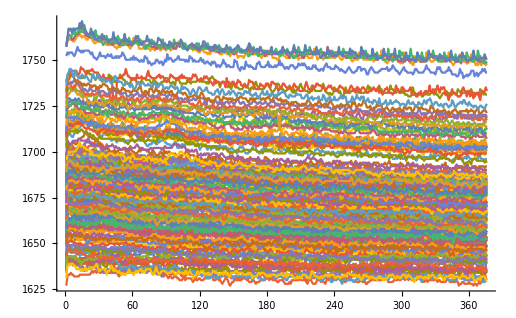

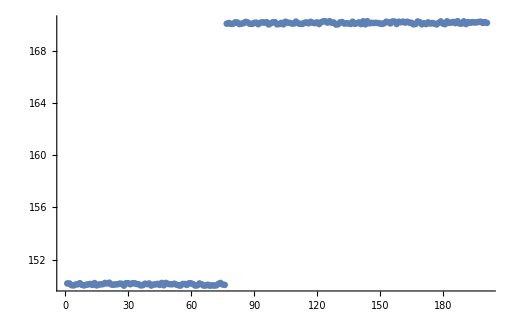

```mathematica
ListLinePlot[schrom, PlotRange->All]
ListPlot[vols, PlotRange -> All]
```

```mathematica
(*This block prints the files which have an error that causes a very low or very high volume, these files should be put in the 'Bad Chroms' folder*)
Do[If[vols[[i]]>800,Print[chromnos[[i]]]],{i,Length[vols]}]
Do[If[vols[[i]]<5,Print[chromnos[[i]]]],{i,Length[vols]}]
```

Section 4.2

### This section finds the peaks in the sample chromatograms using a peak finding function. There is also a function to estimate the background. Plotted below are the plots of all the peaks in the samples, along with the peak position of the calibration peaks. The position of the calibration peak is subtracted and the peaks around 0 are plotted as a histogram - this allows us to select the isoprene peak as it is the one closest to the calibration peak. This corrects for any drift in calibration, or if there are multiple peaks with similar retention times

```mathematica
sampposs= Table[{{}},{i,Length[schrom]}];
```

```mathematica
Monitor[Do[rawchrom= schrom[[isamp]];
dumxxb=EstimatedBackground[rawchrom,30];
dumxx1=rawchrom-dumxxb;
peaktable=N[FindPeaks[dumxx1,5]];
bigpeaktable={};
Do[If[peaktable[[i,2]]>5,bigpeaktable=Append[bigpeaktable,peaktable[[i]]]],{i,Length[peaktable]}];
sampposs[[isamp]]=Table[{timesab[[isamp]],bigpeaktable[[i,1]]},{i,Length[bigpeaktable]}];x1x=N[isamp/Length[sampnos]];,{isamp,Length[schrom]}],ProgressIndicator[x1x]]
```

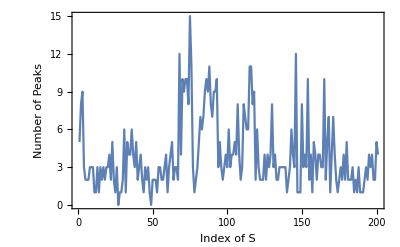

```mathematica
ListLinePlot[Table[Length[sampposs[[i]]],{i,Length[sampposs]}],PlotRange->All,Frame->{{True,False},{True,False}}, FrameLabel->{Style["Index of S",Black,Medium],Style["Number of Peaks",Black,Medium]}]
```

```mathematica
nodata={};
Do[If[Length[sampposs[[i]]]<1,nodata=Append[nodata,i]],{i,Length[sampposs]}]
nodata
```

{27,49}

```mathematica
(*This variable is a list of all the peaks in every chromatogram as a list of [chrom time, retention time]*)
allpeakspostime=Partition[Flatten[sampposs],2];
```

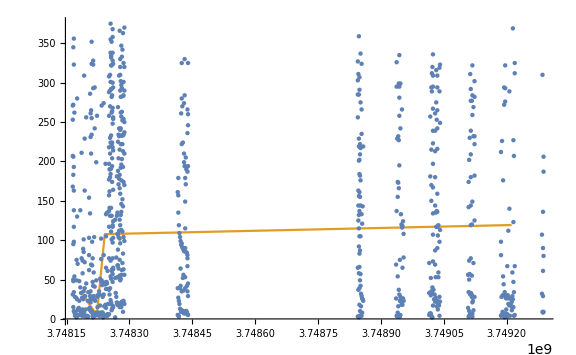

```mathematica
(*This useful plot is of all the peaks in every chromatogram, plotting chrom time(x) and retention time(y) - the gold line is the cal peaks - this lets you see the drift*)
ListPlot[{allpeakspostime,calposabs}, Joined->{False, True},ImageSize->Large]
```

```mathematica
corrpos=allpeakspostime;
```

```mathematica
(*These find the minimum and maximun retention times of all the peaks*)
m1s=Min[Transpose[corrpos][[2]]]
m2s=Max[Transpose[corrpos][[2]]]
```

2.

375.

```mathematica
spreads = IntegerPart[m2s-m1s];
(*This line takes the retention time of the cal-peak from every point's retention time - hence the isoprene peak becomes linear - it essentially removes the drift effects*)
Do[corrpos[[i,2]]=allpeakspostime[[i,2]]-calposabsi[allpeakspostime[[i,1]]],{i,Length[allpeakspostime]}]
(*Hence - xxxts is now a drift-corrected set of values of form [chrom time, drift-corrected retention time]*)
```

InterpolatingFunction::dmval: Input value {3748164936} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

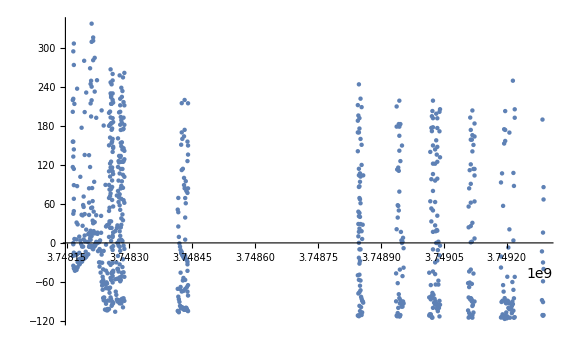

```mathematica
ListPlot[corrpos,ImageSize->Large]
```

```mathematica
posonlys=Table[corrpos[[i,2]],{i,Length[corrpos]}];
```

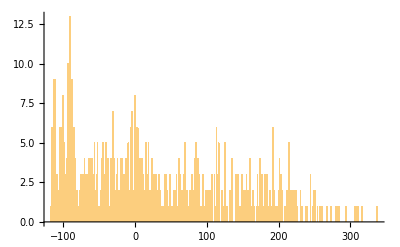

```mathematica
(*This is a histogram of the frequency of measurements at each corrected retention time with the spread defining the bin width*)
Histogram[posonlys,spreads]
```

```mathematica
dummys = HistogramList[posonlys,spreads];
```

```mathematica
(*This variable is a table of the frequency of the peak retention time occuring*)
peakxs = Table[{(dummys[[1,i]]+dummys[[1,i+1]])/2.,dummys[[2,i]]},{i,Length[dummys[[2]]]}];
```

```mathematica
(*This variable is an indexed list of all the corrected peak retention times, with a mean filter of 2 values*)
peakx2s= Table[{i,(dummys[[1,i]]+dummys[[1,i+1]])/2.},{i,Length[dummys[[2]]]}];
```

```mathematica
(*This is a mean filtered version of that histogram*)
peakx1s=MeanFilter[ Table[dummys[[2,i]],{i,Length[dummys[[2]]]}],15];
```

```mathematica
peakx2is=Interpolation[peakx2s,InterpolationOrder->1];
```

```mathematica
(*This blocks defines the sensitivity of function FindPeak. It decides what peak heigh constitutes a peak. The lower the value of 'sg' the more sensitive. A standard value is 10.*)
sg = 10;
pkss=N[FindPeaks[peakx1s,sg]];
pks1s=Table[{peakx2is[pkss[[i,1]]],pkss[[i,2]]},{i,Length[pkss]}];
```

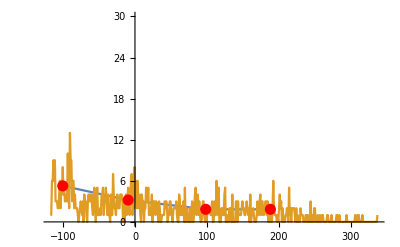

```mathematica
(*This plots the drift-corrected retention time against the peak heights with a corrected baseline removed*)
ListLinePlot[{pks1s,peakxs},PlotRange->{All,{0,30}},Epilog-> {Red,PointSize[0.02],Point[pks1s]}]
```

Section 4.3

### This section integrates the selected parts of the chromatogram to obtain the data on all the peaks with a Gaussian fit. The number of the peaks that it picks can be decided. The output CSV "peak_data_S.csv" has all this data in it.

```mathematica
(*cals=Table[{resultsc[[i,2]],resultsc[[i,6]]},{i,Length[cno]}];*)
```

```mathematica
Clear[ncentre]
```

```mathematica
(*This function looks for the extrapolated points and sets them to the first or last calibration positions*)
ncentre[n_]:=If[n<cno[[1]],scentre=cno[[1]], If[n>cno[[-1]],scentre=cno[[-1]],scentre=n]]
```

```mathematica
resultss=Table[{},{i,Length[sampnos ]}];
```

```mathematica
Monitor[Do[dl=calposindexi[N[ncentre[sampnos[[jj]]]]]-20;
dh=calposindexi[N[ncentre[sampnos[[jj]]]]]+20;
mns=Mean[schrom[[jj]]];
ff=FindFit[schrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mns-200<a<mns+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeaks= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[schrom[[jj]]]}];
fitbases= Table[af+bf*i+bbf*i^2,{i,Length[schrom[[jj]]]}];
fitted = fitpeaks-fitbases;
measured = schrom[[jj]]-fitbases;
area=Mean[fitpeaks]-Mean[fitbases];
residual=schrom[[jj]]-fitpeaks;
rms=StandardDeviation[residual];
scatterdata=Table[{fitted[[ii]],measured[[ii]]},{ii,Length[fitpeaks]}];
lm=LinearModelFit[scatterdata,x,x];
graderr = lm["ParameterTable"][[1,1,3,3]];
(*These lines add a Igor-compatable datetime format*)
timesigor = Table[DateString[timesab[[jj]],{"Day", "/","Month","/","Year", " ", "Hour", ":", "Minute", ":", "Second"}],{jj,Length[timesab]}];
resultss[[jj]]=Flatten[{sampnos[[jj]],timesab[[jj]],timesigor[[jj]],chromnos[[jj]],vols[[jj]],df,cf,ef,area,graderr,rms}];x1=N[jj/Length[sampnos]];,{jj,Length[sampnos ]}],ProgressIndicator[x1]]
```

FindFit::acceptlev: Solved to acceptable level.

General::stop: Further output of FindFit::acceptlev will be suppressed during this calculation.

```mathematica
headers = {"3Index", "3Abs_Time","3Igor_time", "3Chrom_No", "3Volume", "3Position", "3Peak_Height", "3Peak_Width","3Peak_Area",  "3Gradient_Error", "3Root_Mean_Square_Error"};
headedoutputs = Prepend[resultss,headers];
Export["Peak_Data_S.csv", headedoutputs];
```

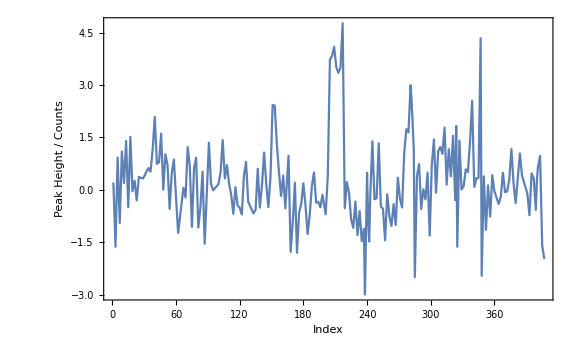

```mathematica
ListLinePlot[{Table[{resultss[[i,1]],resultss[[i,7]]},{i,Length[sampnos]}]},PlotRange->All,ImageSize->Large,
Frame->{{True,False},{True,False}}, FrameLabel->{Style["Index",Black,Medium],Style["Peak Height / Counts",Black,Medium]}]
```

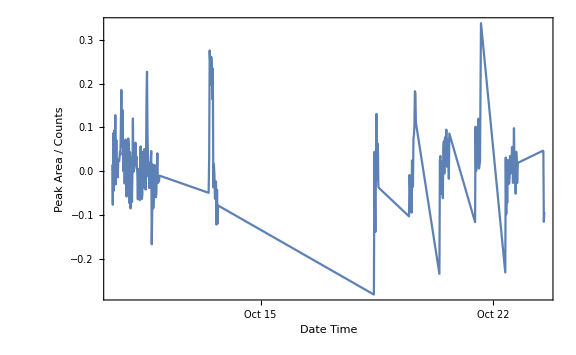

```mathematica
DateListPlot[{Table[{resultss[[i,2]],resultss[[i,9]]},{i,Length[sampnos]}]},PlotRange->All,ImageSize->Large,
Frame->{{True,False},{True,False}}, FrameLabel->{Style["Date Time",Black,Medium],Style["Peak Area / Counts",Black,Medium]}]
```

Section 4.4

### This section takes the isoprene peak height data and interpolates using the calibration curve to obtain the isoprene mixing ratio in ppb. The CSV output is "Isoprene_ppb_S.csv" and contains that data.

```mathematica
(*Now im going to calculate ppb for isoprene, this involves taking the slope of the calibration curve calculated earlier and multiplying the peak height of isoprene divided by the volume*)
```

```mathematica
isoppbs= Table[{},{i,Length[resultss]}];
```

```mathematica
Do[isoppbs[[j]]={resultss[[j,2]], resultss[[j,3]],resultss[[j,4]], resultss[[j,5]],resultss[[j,7]],resultss[[j,9]],((phaf + phbf*resultss[[j,7]]+phcf*resultss[[j,7]]^2)/resultss[[j,5]]),((aaf + abf*resultss[[j,9]] +acf*resultss[[j,9]]^2)/resultss[[j,5]])},{j,Length[resultss]}]
```

```mathematica
isoppbs[[1;;5]]//TableForm
```

3748164936 | 10/10/2018 12:55:36 | 40149 | 150.18 | 0.215298 | 0.0152199 | 0.252651 | 0.42601
3748166200 | 10/10/2018 13:16:40 | 40151 | 150.18 | -1.62651 | -0.0766733 | -0.762743 | -0.186274
3748167473 | 10/10/2018 13:37:53 | 40153 | 150.05 | 0.927134 | 0.0872298 | 0.602975 | 0.861215
3748168771 | 10/10/2018 13:59:31 | 40155 | 150.03 | -0.947127 | -0.0446484 | -0.370044 | 0.0345084
3748170087 | 10/10/2018 14:21:27 | 40157 | 150.1 | 1.09869 | 0.093094 | 0.683566 | 0.894573

```mathematica
headers={"3Abs_Time", "3Igor_time", "3Chrom_No", "3Volume", "3Isoprene_PH","3Isoprene_Area", "3Isoprene_PH_ppb","3Isoprene_Area_ppb"};
headedisoppbs = Prepend[isoppbs,headers];
Export["Isoprene_ppb_S.csv", headedisoppbs];
```

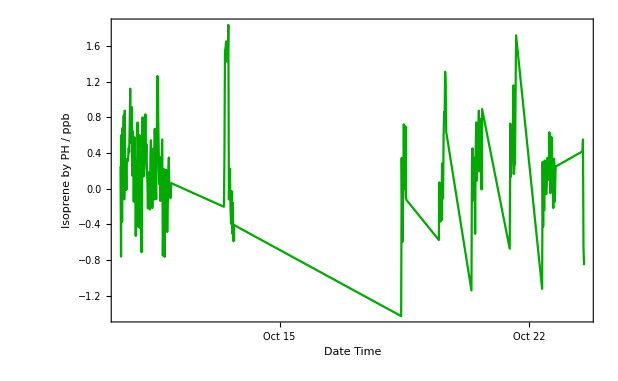

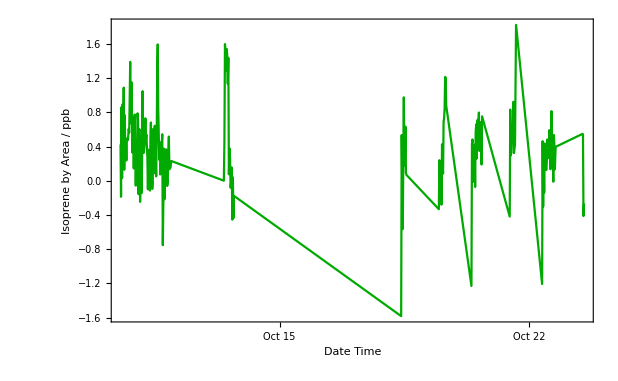

```mathematica
DateListPlot[Table[{isoppbs[[i,1]],isoppbs[[i,7]]},{i,Length[isoppbs]}],PlotStyle->{Darker[Green]},PlotRange-> All,Frame->{{True,False},{True,False}}, FrameLabel->{Style["Date Time",Black,Medium],Style["Isoprene by PH / ppb",Black,Medium]}]

DateListPlot[Table[{isoppbs[[i,1]],isoppbs[[i,8]]},{i,Length[isoppbs]}],PlotStyle->{Darker[Green]},PlotRange-> All,Frame->{{True,False},{True,False}}, FrameLabel->{Style["Date Time",Black,Medium],Style["Isoprene by Area / ppb",Black,Medium]}]
```

Section 4.5

### This section allows you to take individual chromatograms and visually inspect the fitting curve for the data - useful for error checking. This allows you to interrogate suspect points. Simply change the value of variable "jj" which is the chromatogram index. The first two lines tell you the index number highest and lowest points in the data set.

```mathematica
(*This block examines the smallest and largest peaks in the time series*)
Print["The position (j) of the highest isoprene concentration is: ",highests=Position[isoppbs[[;;,6]],Max[isoppbs[[;;,6]]]]]
Print["The Chrom Number is: ", isoppbs[[highests[[1,1]],3]]]
Print["The position of the lowest isoprene concentration is: ",lowests=Position[isoppbs[[;;,6]],Min[isoppbs[[;;,6]]]]]
Print["The Chrom Number is: ", isoppbs[[lowests[[1,1]],3]]]
```

The position (j) of the highest isoprene concentration is: {{171}}

The Chrom Number is: 40565

The position of the lowest isoprene concentration is: {{113}}

The Chrom Number is: 40418

The number of the Chromatogram is: 95

The chrom number of the Chromatogram is: 40372

The time of the Chromatogram is: 13/10/2018 10:50:11

The fitting curve looks like this:

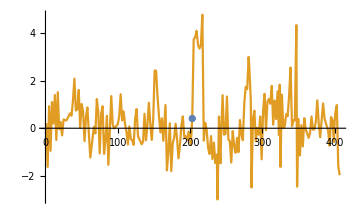
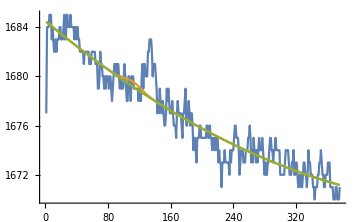

```mathematica
jj=95;
dl=calposindexi[N[ncentre[sampnos[[jj]]]]]-20;
dh=calposindexi[N[ncentre[sampnos[[jj]]]]]+20;
mnx=Mean[schrom[[jj]]];
ff=FindFit[schrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mnx-200<a<mnx+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeaks= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[schrom[[jj]]]}];
fitbases= Table[af+bf*i+bbf*i^2,{i,Length[schrom[[jj]]]}];
fitted = fitpeaks-fitbases;
measured = schrom[[jj]]-fitbases;
area=Mean[fitpeaks]-Mean[fitbases];
residual=schrom[[jj]]-fitpeaks;
rms=StandardDeviation[residual];
scatterdata=Table[{fitted[[ii]],measured[[ii]]},{ii,Length[fitpeaks]}];
lm=LinearModelFit[scatterdata,x,x];
graderr = lm["ParameterTable"][[1,1,3,3]];
(*These lines add a Igor-compatable datetime format*)
timesigor = Table[DateString[timesab[[jj]],{"Day", "/","Month","/","Year", " ", "Hour", ":", "Minute", ":", "Second"}],{jj,Length[timesab]}];
resultss[[jj]]=Flatten[{sampnos[[jj]],timesab[[jj]],timesigor[[jj]],chromnos[[jj]],vols[[jj]],df,cf,ef,area,graderr,rms}];

Print["The number of the Chromatogram is: ",jj]
Print["The chrom number of the Chromatogram is: ",chromnos[[jj]]]
Print["The time of the Chromatogram is: ",timesigor[[jj]]]
Print["The fitting curve looks like this: "]
datapoint={{sampnos[[jj]],cf}};
{ListLinePlot[{datapoint,Table[{resultss[[i,1]],resultss[[i,7]]},{i,Length[sampnos]}]},PlotRange->All,ImageSize->Medium,Joined->{False,True}],ListLinePlot[{schrom[[jj]],fitpeaks,fitbases},PlotRange->All,ImageSize->Medium]}
```

## Section 5: Sample 2 (X) Chromatograms

### This section - Takes the sample 2 chromatograms, labelled 'X' - Plots them - Determines the number of peaks in each chromatogram - Plots the locations of all the peaks in each chromatogram - Corrects the drift by subtracting the position of the nearest-in-time calibration peak - From a histogram of peak locations, the major peaks in the time series are identified - These peaks are then subtracted from a calculated background and integrated - The peaks are plotted, the date are tabulated and exported - The peak height values are converted to mixing ratio using the calibration curves - The mixing ratio data is exported

Section 5.1 :

### Select the Sample 2 (X) Chromatograms and plot them, along with the sample volume to diagnose errors. The bottom two lines check the chromatogram number of the error files.

```mathematica
sampnox = {};
```

```mathematica
Do[If[type[[i]]=="X",sampnox = Append[sampnox,i]],{i,nn}]
```

```mathematica
volx = Table[{},{i,Length[sampnox]}];
xchrom= Table[{},{i,Length[sampnox]}];
chromnox = Table[{},{i,Length[sampnox]}];
timex= Table[{},{i,Length[sampnox]}];
```

```mathematica
Do[dumx = data[[sampnox[[i]]]];
xchrom[[i]]=Table[dumx[[j,2]],{j,17+off,Length[dumx]}];
volx[[i]]=dumx[[11,2]];
chromnox[[i]]=dumx[[1, 2]];
timex[[i]]  =dumx[[2,2;;7]];,{i,Length[sampnox]}]
```

```mathematica
timexab=Table[AbsoluteTime[timex[[i]]],{i,Length[timex]}];
timexday=(timexab-timexab[[1]])/24./3600;
```

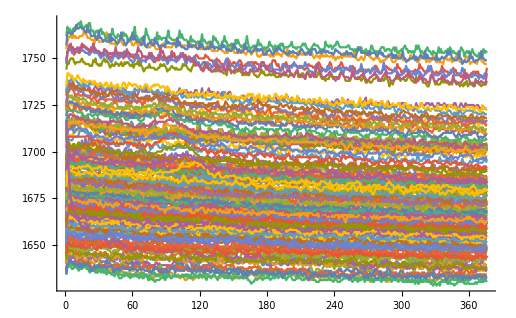

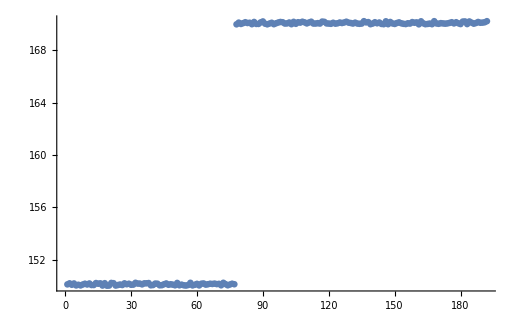

```mathematica
ListLinePlot[xchrom, PlotRange->All]
ListPlot[volx, PlotRange -> All]
```

```mathematica
(*This block prints the files which have an error that causes a very low or very high volume, these files should be put in the 'Bad Chroms' folder*)
Do[If[volx[[i]]>800,Print[chromnox[[i]]]],{i,Length[volx]}]
Do[If[volx[[i]]<5,Print[chromnox[[i]]]],{i,Length[volx]}]
```

Section 5.2

### This section finds the peaks in the sample chromatograms using a peak finding function. There is also a function to estimate the background. Plotted below are the plots of all the peaks in the samples, along with the peak position of the calibration peaks. The position of the calibration peak is subtracted and the peaks around 0 are plotted as a histogram - this allows us to select the isoprene peak as it is the one closest to the calibration peak. This corrects for any drift in calibration, or if there are multiple peaks with similar retention timex

```mathematica
sampposx= Table[{{}},{i,Length[xchrom]}];
```

```mathematica
Monitor[Do[rawchrom= xchrom[[isamp]];
dumxxb=EstimatedBackground[rawchrom,30];
dumxx1=rawchrom-dumxxb;
peaktable=N[FindPeaks[dumxx1,5]];
bigpeaktable={};
Do[If[peaktable[[i,2]]>5,bigpeaktable=Append[bigpeaktable,peaktable[[i]]]],{i,Length[peaktable]}];
sampposx[[isamp]]=Table[{timexab[[isamp]],bigpeaktable[[i,1]]},{i,Length[bigpeaktable]}];x1x=N[isamp/Length[sampnox]];,{isamp,Length[xchrom]}],ProgressIndicator[x1x]]
```

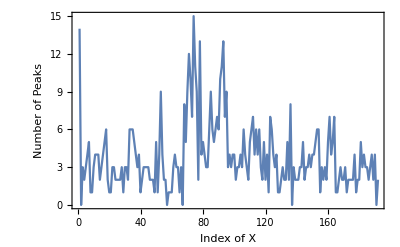

```mathematica
ListLinePlot[Table[Length[sampposx[[i]]],{i,Length[sampposx]}],PlotRange->All,Frame->{{True,False},{True,False}}, FrameLabel->{Style["Index of X",Black,Medium],Style["Number of Peaks",Black,Medium]}]
```

```mathematica
nodata={};
Do[If[Length[sampposx[[i]]]<1,nodata=Append[nodata,i]],{i,Length[sampposx]}]
nodata
```

{2,57,67,137,191}

```mathematica
(*This variable is a list of all the peaks in every chromatogram as a list of [chrom time, retention time]*)
allpeakxpostime=Partition[Flatten[sampposx],2];
```

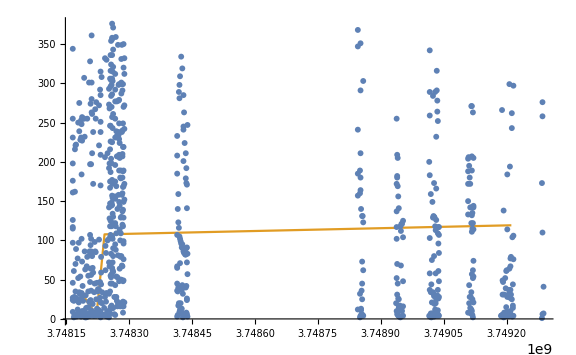

```mathematica
(*This useful plot is of all the peaks in every chromatogram, plotting chrom time(x) and retention time(y) - the gold line is the cal peaks - this lets you see the drift*)
ListPlot[{allpeakxpostime,calposabs}, Joined->{False, True},ImageSize->Large]
```

```mathematica
corrpos=allpeakxpostime;
```

```mathematica
(*These find the minimum and maximun retention timex of all the peaks*)
m1x=Min[Transpose[corrpos][[2]]]
m2x=Max[Transpose[corrpos][[2]]]
```

1.

376.

```mathematica
spreadx = IntegerPart[m2x-m1x];
(*This line takes the retention time of the cal-peak from every point's retention time - hence the isoprene peak becomes linear - it essentially removes the drift effects*)
Do[corrpos[[i,2]]=allpeakxpostime[[i,2]]-calposabsi[allpeakxpostime[[i,1]]],{i,Length[allpeakxpostime]}]
(*Hence - xxxts is now a drift-corrected set of values of form [chrom time, drift-corrected retention time]*)
```

InterpolatingFunction::dmval: Input value {3748165563} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

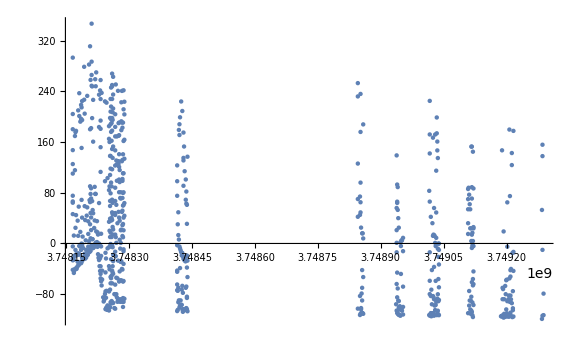

```mathematica
ListPlot[corrpos,ImageSize->Large]
```

```mathematica
posonlyx=Table[corrpos[[i,2]],{i,Length[corrpos]}];
```

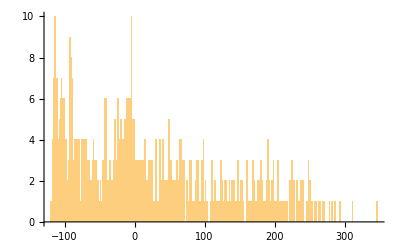

```mathematica
(*This is a histogram of the frequency of measurements at each corrected retention time with the spread defining the bin width*)
Histogram[posonlyx,spreadx]
```

```mathematica
dummyx= HistogramList[posonlyx,spreadx];
```

```mathematica
(*This variable is a table of the frequency of the peak retention time occuring*)
peakxx = Table[{(dummyx[[1,i]]+dummyx[[1,i+1]])/2.,dummyx[[2,i]]},{i,Length[dummyx[[2]]]}];
```

```mathematica
(*This variable is an indexed list of all the corrected peak retention timex, with a mean filter of 2 values*)
peakx2x= Table[{i,(dummyx[[1,i]]+dummyx[[1,i+1]])/2.},{i,Length[dummyx[[2]]]}];
```

```mathematica
(*This is a mean filtered version of that histogram*)
peakx1x=MeanFilter[ Table[dummyx[[2,i]],{i,Length[dummyx[[2]]]}],15];
```

```mathematica
peakx2ix=Interpolation[peakx2x,InterpolationOrder->1];
```

```mathematica
(*This blocks defines the sensitivity of function FindPeak. It decides what peak heigh constitutes a peak. The lower the value of 'sg' the more sensitive. A standard value is 10.*)
sg = 10;
pksx=N[FindPeaks[peakx1x,sg]];
pks1x=Table[{peakx2ix[pksx[[i,1]]],pksx[[i,2]]},{i,Length[pksx]}];
```

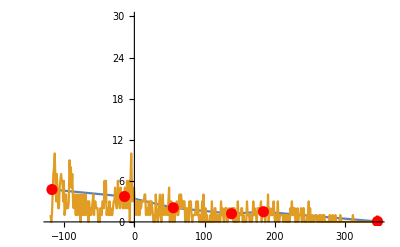

```mathematica
(*This plots the drift-corrected retention time against the peak heights with a corrected baseline removed*)
ListLinePlot[{pks1x,peakxx},PlotRange->{All,{0,30}},Epilog-> {Red,PointSize[0.02],Point[pks1x]}]
```

Section 5.3

### This section integrates the selected parts of the chromatogram to obtain the data on all the peaks with a Gaussian fit. The number of the peaks that it picks can be decided. The output CSV "peak_data_S.csv" has all this data in it.

```mathematica
(*cals=Table[{resultsc[[i,2]],resultsc[[i,6]]},{i,Length[cno]}];*)
```

```mathematica
Clear[ncentre]
```

```mathematica
(*This function looks for the extrapolated points and sets them to the first or last calibration positions*)
ncentre[n_]:=If[n<cno[[1]],xcentre=cno[[1]], If[n>cno[[-1]],xcentre=cno[[-1]],xcentre=n]]
```

```mathematica
resultsx=Table[{},{i,Length[sampnox ]}];
```

```mathematica
Monitor[Do[dl=calposindexi[N[ncentre[sampnox[[jj]]]]]-20;
dh=calposindexi[N[ncentre[sampnox[[jj]]]]]+20;
mnx=Mean[xchrom[[jj]]];
ff=FindFit[xchrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mnx-200<a<mnx+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeakx= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[xchrom[[jj]]]}];
fitbasex= Table[af+bf*i+bbf*i^2,{i,Length[xchrom[[jj]]]}];
fittedx = fitpeakx-fitbasex;
measuredx = xchrom[[jj]]-fitbasex;
areax=Mean[fitpeakx]-Mean[fitbasex];
residualx=xchrom[[jj]]-fitpeakx;
rmsx=StandardDeviation[residualx];
scatterdatax=Table[{fittedx[[ii]],measuredx[[ii]]},{ii,Length[fitpeakx]}];
lmx=LinearModelFit[scatterdatax,x,x];
graderrx = lmx["ParameterTable"][[1,1,3,3]];
(*These lines add a Igor-compatable datetime format*)
timexigor = Table[DateString[timexab[[jj]],{"Day", "/","Month","/","Year", " ", "Hour", ":", "Minute", ":", "Second"}],{jj,Length[timexab]}];
resultsx[[jj]]=Flatten[{sampnox[[jj]],timexab[[jj]],timexigor[[jj]],chromnox[[jj]],volx[[jj]],df,cf,ef,areax,graderrx,rmsx}];x1=N[jj/Length[sampnox]];,{jj,Length[sampnox ]}],ProgressIndicator[x1]]
```

FindFit::acceptlev: Solved to acceptable level.

General::stop: Further output of FindFit::acceptlev will be suppressed during this calculation.

```mathematica
headerx = {"4Index", "4Abs_Time","4Igor_time", "4Chrom_No", "4Volume", "4Position", "4Peak_Height", "4Peak_Width","4Peak_Area",  "4Gradient_Error", "4Root_Mean_Square_Error"};
headedoutputx = Prepend[resultsx,headerx];
Export["Peak_Data_X.csv", headedoutputx];
```

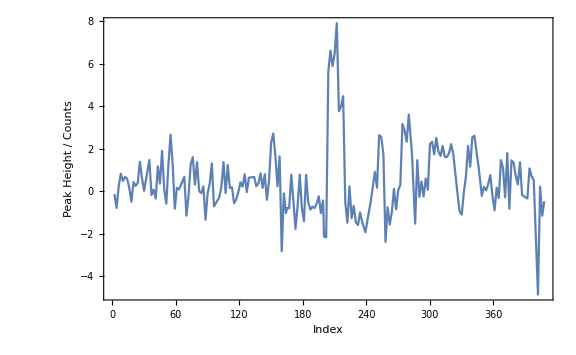

```mathematica
ListLinePlot[{Table[{resultsx[[i,1]],resultsx[[i,7]]},{i,Length[sampnox]}]},PlotRange->All,ImageSize->Large,
Frame->{{True,False},{True,False}}, FrameLabel->{Style["Index",Black,Medium],Style["Peak Height / Counts",Black,Medium]}]
```

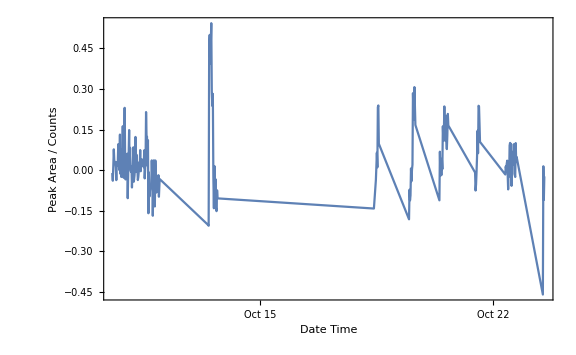

```mathematica
DateListPlot[{Table[{resultsx[[i,2]],resultsx[[i,9]]},{i,Length[sampnox]}]},PlotRange->All,ImageSize->Large,
Frame->{{True,False},{True,False}}, FrameLabel->{Style["Date Time",Black,Medium],Style["Peak Area / Counts",Black,Medium]}]
```

Section 5.4

### This section takes the isoprene peak height data and interpolates using the calibration curve to obtain the isoprene mixing ratio in ppb. The CSV output is "Isoprene_ppb_S.csv" and contains that data.

```mathematica
(*Now im going to calculate ppb for isoprene, this involves taking the slope of the calibration curve calculated earlier and multiplying the peak height of isoprene divided by the volume*)
```

```mathematica
isoppbx= Table[{},{i,Length[resultsx]}];
```

```mathematica
Do[isoppbx[[j]]={resultsx[[j,2]], resultsx[[j,3]],resultsx[[j,4]], resultsx[[j,5]],resultsx[[j,7]],resultsx[[j,9]],((phaf + phbf*resultsx[[j,7]]+phcf*resultsx[[j,7]]^2)/resultsx[[j,5]]),((aaf + abf*resultsx[[j,9]] +acf*resultsx[[j,9]]^2)/resultsx[[j,5]])},{j,Length[resultsx]}]
```

```mathematica
headers={"1Abs_Time", "1Igor_time", "1Chrom_No", "1Volume", "1Isoprene_PH","1Isoprene_Area", "1Isoprene_PH_ppb","1Isoprene_Area_ppb"};
headedisoppbs = Prepend[isoppbx,headers];
Export["Isoprene_ppb_X.csv", headedisoppbs];
```

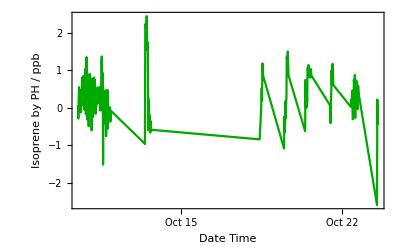

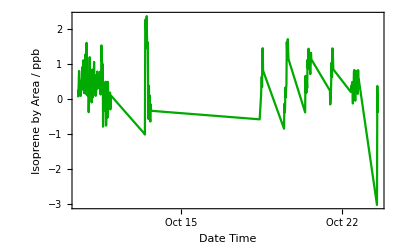

```mathematica
DateListPlot[Table[{isoppbx[[i,1]],isoppbx[[i,7]]},{i,Length[isoppbx]}],PlotStyle->{Darker[Green]},PlotRange-> All,Frame->{{True,False},{True,False}}, FrameLabel->{Style["Date Time",Black,Medium],Style["Isoprene by PH / ppb",Black,Medium]}]

DateListPlot[Table[{isoppbx[[i,1]],isoppbx[[i,8]]},{i,Length[isoppbx]}],PlotStyle->{Darker[Green]},PlotRange-> All,Frame->{{True,False},{True,False}}, FrameLabel->{Style["Date Time",Black,Medium],Style["Isoprene by Area / ppb",Black,Medium]}]
```

Section 5.5

### This section allows you to take individual chromatograms and visually inspect the fitting curve for the data - useful for error checking. This allows you to interrogate suspect points. Simply change the value of variable "jj" which is the chromatogram index. The first two lines tell you the index number highest and lowest points in the data set.

```mathematica
(*This block examines the smallest and largest peaks in the time series*)
Print["The position (j) of the highest isoprene concentration is: ",highestx=Position[isoppbx[[;;,6]],Max[isoppbx[[;;,6]]]]]
Print["The Chrom Number is: ", isoppbx[[highestx[[1,1]],3]]]
Print["The position of the lowest isoprene concentration is: ",lowestx=Position[isoppbx[[;;,6]],Min[isoppbx[[;;,6]]]]]
Print["The Chrom Number is: ", isoppbx[[lowestx[[1,1]],3]]]
```

The position (j) of the highest isoprene concentration is: {{101}}

The Chrom Number is: 40381

The position of the lowest isoprene concentration is: {{189}}

The Chrom Number is: 40635

The number of the Chromatogram is: 40

The fitting curve looks like this:

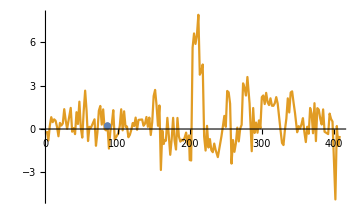
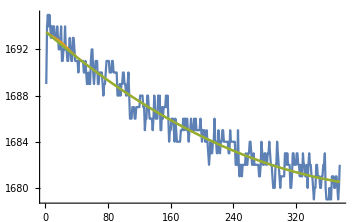

```mathematica
jj=40;
dl=calposindexi[N[ncentre[sampnox[[jj]]]]]-20;
dh=calposindexi[N[ncentre[sampnox[[jj]]]]]+20;
mnx=Mean[xchrom[[jj]]];
ff=FindFit[xchrom[[jj]],{a+b*i+bb*i^2+c*Exp[-((d-i)/e)^2],{mnx-200<a<mnx+200,-10<b<10,-10<bb<10,dl<d<dh,20>e>10}},{a,b,bb,c,d,e},i];
af = ff[[1,2]];bf = ff[[2,2]];bbf = ff[[3,2]];cf = ff[[4,2]];df = ff[[5,2]];ef = ff[[6,2]];
fitpeakx= Table[af+bf*i+bbf*i^2+cf*Exp[-((df-i)/ef)^2],{i,Length[xchrom[[jj]]]}];
fitbasex= Table[af+bf*i+bbf*i^2,{i,Length[xchrom[[jj]]]}];
fittedx = fitpeakx-fitbasex;
measuredx = xchrom[[jj]]-fitbasex;
areax=Mean[fitpeakx]-Mean[fitbasex];
residualx=xchrom[[jj]]-fitpeakx;
rmsx=StandardDeviation[residualx];
scatterdatax=Table[{fittedx[[ii]],measuredx[[ii]]},{ii,Length[fitpeakx]}];
lmx=LinearModelFit[scatterdatax,x,x];
graderrx = lmx["ParameterTable"][[1,1,3,3]];
(*These lines add a Igor-compatable datetime format*)
timexigor = Table[DateString[timexab[[jj]],{"Day", "/","Month","/","Year", " ", "Hour", ":", "Minute", ":", "Second"}],{jj,Length[timexab]}];
resultsx[[jj]]=Flatten[{sampnox[[jj]],timexab[[jj]],timexigor[[jj]],chromnox[[jj]],volx[[jj]],df,cf,ef,areax,graderrx,rmsx}];

Print["The number of the Chromatogram is: ",jj]
Print["The fitting curve looks like this: "]
datapointx={{sampnox[[jj]],cf}};
{ListLinePlot[{datapointx,Table[{resultsx[[i,1]],resultsx[[i,7]]},{i,Length[sampnox]}]},PlotRange->All,ImageSize->Medium,Joined->{False,True}],ListLinePlot[{xchrom[[jj]],fitpeakx,fitbasex},PlotRange->All,ImageSize->Medium]}
```